## Podaci za rast tumora (tumorskog sferoida)

```mathematica
data=
{{4.56,       0.0016308  },
{5.66,           0.0032148  },  
{6.68,           0.005614  }, 
{7.89,         0.0118598  },
{8.81,         0.02015  },
{9.79,         0.027538  },
{10.99,       0.034546  },
{11.99,       0.06608  },
{12.86,       0.078932  },
{15.17,     0.155  },
{16.17,     0.23144  },
{17.41,     0.33438  },
{18.33,     0.56514  },
{19.37,     0.72128  },
{20.40,     0.708946  },
{22.15,   1.08536  },
{23.16,   2.1296  },
{24.01,   2.0304  },
{25.22,   2.4478  },
{27.52,   2.7564  },
{28.27,   2.714  },
{29.26,   2.9056  },
{30.31,   3.4054  },
{31.41,   3.9004  },
{32.36,   4.914  },
{33.36,   5.6692  },
{34.29,   5.8266  },
{36.18,   6.1494  },
{38.19,   7.1194  },
{39.98,   9.0246  },
{42.08, 10.8542  },
{44.39, 12.050  },
{45.44, 10.7492  },
{46.33, 13.342  },
{47.38, 15.646  },
{48.73, 17.126  },
{51.08, 13.2466  },
{52.15, 14.938  },
{53.09, 17.660  },
{55.10, 19.030  },
{56.44, 20.272  },
{57.45, 17.346  },
{59.58, 17.510  },
{61.79, 18.790  },
{63.82, 18.518  },
{67.01, 19.186  },
{67.98, 21.640  },
{70.17, 18.446 }}
```

{{4.56,0.0016308},{5.66,0.0032148},{6.68,0.005614},{7.89,0.0118598},{8.81,0.02015},{9.79,0.027538},{10.99,0.034546},{11.99,0.06608},{12.86,0.078932},{15.17,0.155},{16.17,0.23144},{17.41,0.33438},{18.33,0.56514},{19.37,0.72128},{20.4,0.708946},{22.15,1.08536},{23.16,2.1296},{24.01,2.0304},{25.22,2.4478},{27.52,2.7564},{28.27,2.714},{29.26,2.9056},{30.31,3.4054},{31.41,3.9004},{32.36,4.914},{33.36,5.6692},{34.29,5.8266},{36.18,6.1494},{38.19,7.1194},{39.98,9.0246},{42.08,10.8542},{44.39,12.05},{45.44,10.7492},{46.33,13.342},{47.38,15.646},{48.73,17.126},{51.08,13.2466},{52.15,14.938},{53.09,17.66},{55.1,19.03},{56.44,20.272},{57.45,17.346},{59.58,17.51},{61.79,18.79},{63.82,18.518},{67.01,19.186},{67.98,21.64},{70.17,18.446}}

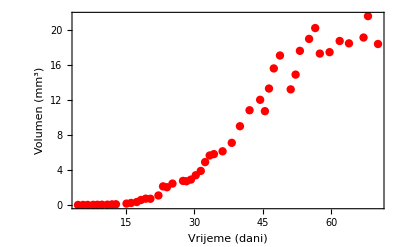

```mathematica
pod=ListPlot[data,Frame->True,FrameLabel->{"Vrijeme (dani)","Volumen (mm^3)"},RotateLabel->True, PlotStyle->{PointSize[0.015],RGBColor[1,0,0]}]
```

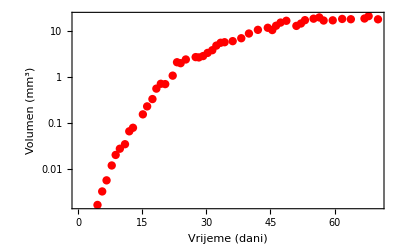

```mathematica
lpod=ListLogPlot[data,Frame->True,FrameLabel->{"Vrijeme (dani)","Volumen (mm^3)"},RotateLabel->True,PlotStyle->{PointSize[0.015],RGBColor[1,0,0]}]
```

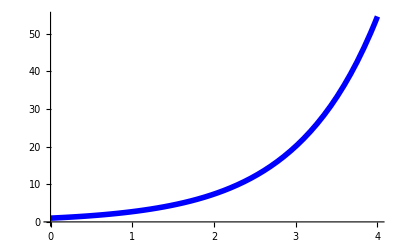

```mathematica
Plot[Exp[x],{x,0,4},PlotStyle->{Thickness[0.01],RGBColor[0,0,1]}]
```

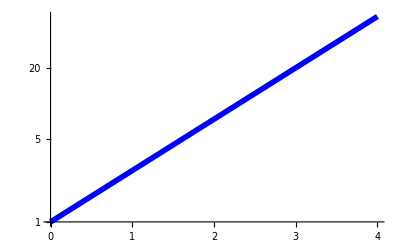

```mathematica
LogPlot[Exp[x],{x,0,4},PlotStyle->{Thickness[0.01],RGBColor[0,0,1]}]
```

## Podaci i logistička krivulja

```mathematica
sol=DSolve[{y'[x]==a y[x] (1- y[x]/c),y[0]==y0},y[x],x]
y[x_,a_,c_,y0_]:= Evaluate[Part[y[x]/.sol,1]];
(* y[x_,a_,c_,y0_]:= c Exp[a x] y0 / ( c - y0 + y0 Exp[a x]) *)
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{y[x]→(c ⅇ^(a x) y0)/(c-y0+ⅇ^(a x) y0)}}

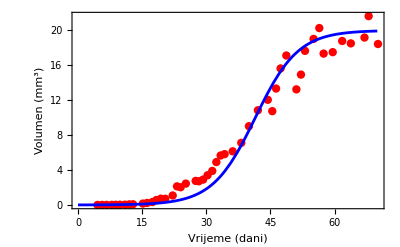

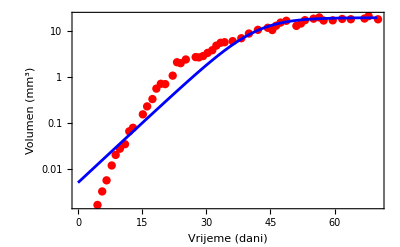

```mathematica
c1=Plot[y[x,0.2,20,0.005],{x,0,70}, PlotRange->{0,25},PlotStyle->{Blue,Thickness->0.005}];
lc1=LogPlot[y[x,0.2,20,0.005],{x,0,70}, PlotRange->{0,25},PlotStyle->{Blue,Thickness->0.005}];
Show[pod,c1]
Show[lpod,lc1]
```

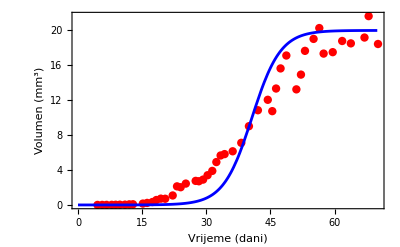

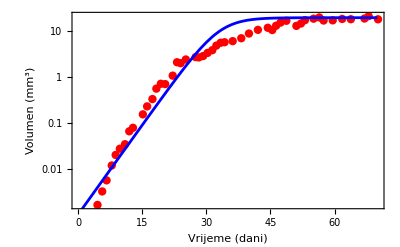

```mathematica
c1=Plot[y[x,0.3,20,0.0001],{x,0,70}, PlotRange->{0,25000},PlotStyle->{Blue,Thickness->0.005}];
lc1=LogPlot[y[x,0.3,20,0.001],{x,0,70}, PlotRange->{0,25000},PlotStyle->{Blue,Thickness->0.005}];
Show[pod,c1]
Show[lpod,lc1]
```

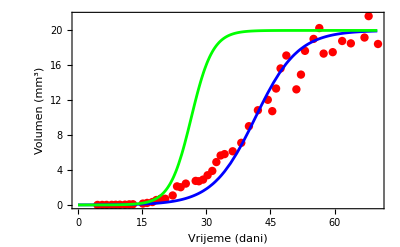

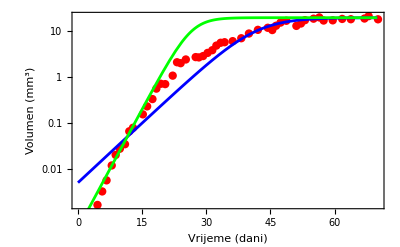

```mathematica
c=Plot[{y[x,0.2,20,0.005],y[x,0.4,20,0.0005]},{x,0,70}, PlotRange->{0,25000},PlotStyle->{{Blue,Thickness->0.005},{Green,Thickness->0.005}}];
lc=LogPlot[{y[x,0.2,20,0.005],y[x,0.4,20,0.0005]},{x,0,70}, PlotRange->{0,25000},PlotStyle->{{Blue,Thickness->0.005},{Green,Thickness->0.005}}];
Show[pod,c]
Show[lpod,lc]
```

## METODA NAJMANJIH KVADRATA

## MNK i logistička krivulja

```mathematica
y[x_,a_,c_,y0_]:= c  y0 / ( (c - y0 )Exp[-a x]+ y0 )
```

```mathematica
par=FindFit[data,y[x,a,c,y0],{{a,0.2},{c,20},{y0,0.1}},x]
```

{a→0.140315,c→20.044,y0→0.0607316}

```mathematica
FindFit[data,y[x,a,c,y0],{a,c,y0},x]
```

{a→37.595,c→7.52904,y0→-999.408}

```mathematica
FindFit[data,{y[x,a,c,y0],{a>0,c>0,y0>0}},{a,c,y0},x]
```

FindFit::eit: The algorithm does not converge to the tolerance of 4.80622×10^-6 in 500 iterations. The best estimated solution, with feasibility residual, KKT residual, or complementary residual of {1.6883859252668828`*^-10, 0.00015249790809036498`, 6.024686776941715`*^-11}, is returned.

{a→0.0417888,c→305.285,y0→1.48366}

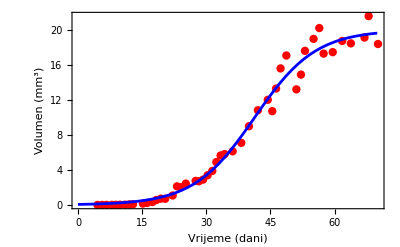

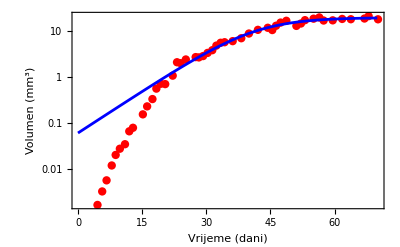

```mathematica
{fa,fc,fy0}={a,c,y0}/. par;c1=Plot[y[x,fa,fc,fy0],{x,0,70}, PlotRange->{0,25000},PlotStyle->{Blue,Thickness->0.005}];
lc1=LogPlot[y[x,fa,fc,fy0],{x,0,70}, PlotRange->{0,25000},PlotStyle->{Blue,Thickness->0.005}];
Show[pod,c1]
Show[lpod,lc1]
```

## Logaritmirani podaci

```mathematica
tdata=Transpose[data];
tt=tdata[[1]];
ty=tdata[[2]];
lny=Log[ty];
tdata[[2]]=lny;
lndata=Transpose[tdata];
```

```mathematica
ly[x_,a_,c_,y0_]:= Log[c  y0 / ( (c - y0 )Exp[-a x]+ y0 )]
```

```mathematica
par1=FindFit[lndata,ly[x,a,c,y0],{{a,0.14},{c,20.04},{y0,0.06}},x]
```

FindFit::nrlnum: The function value {5.68818352830048`  + 3.141592653589793` ⅈ, 5.315089481936825`  + 3.141592653589793` ⅈ, 5.046806503418991`  + 3.141592653589793` ⅈ, « 42 », -0.7701251121070274` + 0.` ⅈ, -0.8904880769517627` + 0.` ⅈ, -0.7307927074661742` + 0.` ⅈ} is not a list of real numbers with dimensions {48} at {a, c, y0} = {0.26125558880189764`, 8.882243205610155`, -0.14101570678470055`}.

{a→0.261256,c→8.88224,y0→-0.141016}

```mathematica
par1=FindFit[lndata,{ly[x,a,c,y0],{a>0}},{{a,0.2},{c,20.04},{y0,1}},x]
```

FindFit::eit: The algorithm does not converge to the tolerance of 4.80622×10^-6 in 500 iterations. The best estimated solution, with feasibility residual, KKT residual, or complementary residual of {1.7654757105361904`*^-13, 0.1098245450605966`, 1.7833087985214046`*^-13}, is returned.

{a→0.304144,c→13.4805,y0→0.00117057}

```mathematica
par1=FindFit[lndata,{ly[x,a,c,y0],{a>0}},{{a,0.2},{c,15},{y0,1}},x]
```

FindFit::eit: The algorithm does not converge to the tolerance of 4.80622×10^-6 in 500 iterations. The best estimated solution, with feasibility residual, KKT residual, or complementary residual of {1.7654935563070561`*^-13, 0.07877434865583968`, 1.7833268245525818`*^-13}, is returned.

{a→0.304147,c→13.4804,y0→0.00117053}

```mathematica
par1=FindFit[lndata,{ly[x,a,c,y0],{a>0}},{{a,0.01},{c,15},{y0,2}},x,MaxIterations->3000]
```

FindFit::eit: The algorithm does not converge to the tolerance of 4.80622×10^-6 in 3000 iterations. The best estimated solution, with feasibility residual, KKT residual, or complementary residual of {1.7628861128138`*^-13, 1.413987748417109`, 1.7806930432462625`*^-13}, is returned.

{a→0.303698,c→13.4965,y0→0.00117729}

```mathematica
par1=FindFit[lndata,{ly[x,a,c,y0],{a>0}},{{a,0.01},{c,15},{y0,2}},x,MaxIterations->6000]
```

FindFit::eit: The algorithm does not converge to the tolerance of 4.80622×10^-6 in 6000 iterations. The best estimated solution, with feasibility residual, KKT residual, or complementary residual of {1.7631183575105974`*^-13, 1.2971789813507464`, 1.7809276338490883`*^-13}, is returned.

{a→0.303738,c→13.4951,y0→0.00117668}

```mathematica
par=FindFit[lndata,{ly[x,a,c,y0],{a>0}},{{a,0.01},{c,15},{y0,2}},x,MaxIterations->20000]
```

FindFit::eit: The algorithm does not converge to the tolerance of 4.80622×10^-6 in 20000 iterations. The best estimated solution, with feasibility residual, KKT residual, or complementary residual of {1.7639589974542958`*^-13, 0.8669829591232476`, 1.7817767651053492`*^-13}, is returned.

{a→0.303882,c→13.4899,y0→0.00117449}

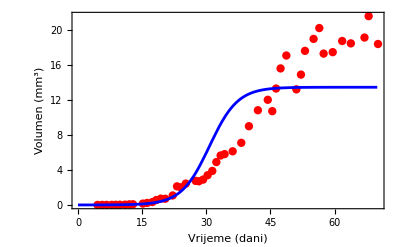

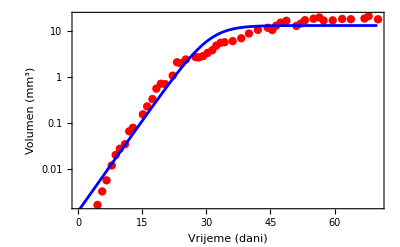

```mathematica
{lfa,lfc,lfy0}={a,c,y0}/. par;c1=Plot[y[x,lfa,lfc,lfy0],{x,0,70}, PlotRange->{0,25000},PlotStyle->{Blue,Thickness->0.005}];
lc1=LogPlot[y[x,lfa,lfc,lfy0],{x,0,70}, PlotRange->{0,25000},PlotStyle->{Blue,Thickness->0.005}];
Show[pod,c1]
Show[lpod,lc1]
```

## Kvadratno odstupanje

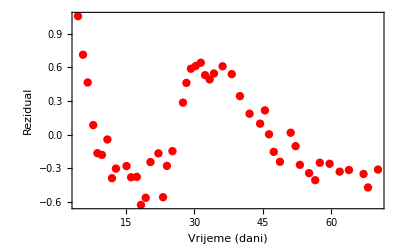

```mathematica
my=ly[tt,lfa,lfc,lfy0];
residual=my-lny;
tmp={tt,residual};
res=Transpose[tmp];
ListPlot[res,Frame->True,FrameLabel->{"Vrijeme (dani)","Rezidual"},RotateLabel->True,PlotStyle->{PointSize[0.015],RGBColor[1,0,0]}]
```

```mathematica
(residual.residual)/Length[residual]
```

0.168612

```mathematica
(residual.residual)/(Length[residual]-3)
```

0.179853

## Podaci i Gompertzova krivulja

```mathematica
DSolve[{y'[x]==a y[x] (1- Log[y[x]]/Log[C]),y[0]==y0},y[x],x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{y[x]→C (y0/C)^(ⅇ^(-(a x)/Log[C]))}}

```mathematica
yg[x_,a_,c_,y0_]:= c Exp[Log[y0/c] Exp[-a x /Log[c]]]
```

```mathematica
lyg[x_,a_,lc_,ly0_]:=lc+(ly0-lc) Exp[-a x /lc]
```

```mathematica
par=FindFit[data,{yg[x,a,c,y0],{c>0,a>0,y0>0}},{{a,0.2},{c,24},{y0,0.0001}},x,MaxIterations->4000]
```

FindFit::eit: The algorithm does not converge to the tolerance of 4.80622×10^-6 in 4000 iterations. The best estimated solution, with feasibility residual, KKT residual, or complementary residual of {0.0013528402597336392`, 0.686230852297927`, 0.0007330695179131245`}, is returned.

{a→0.195448,c→24.5697,y0→0.000367124}

```mathematica
par=FindFit[lndata,{lyg[x,a,c,y0],{a>0,c>0}},{{a,1},{c,30},{y0,5}},x,MaxIterations->10000]
```

{a→0.206226,c→3.18352,y0→-9.68866}

a =0.206226   c = 24.1316 y0 = 0.0000619827

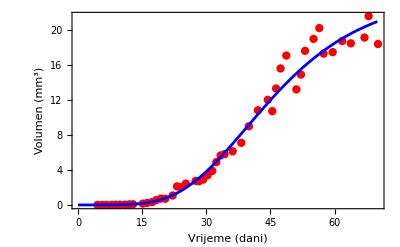

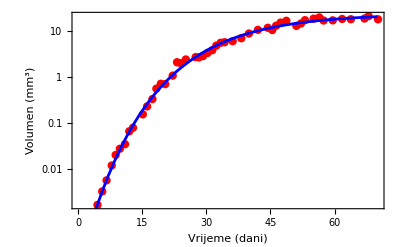

```mathematica
{gfa,gfc,gfy0}={a,c,y0}/. par;
gfec=Exp[gfc]; gfey0=Exp[gfy0];
Print["a =",gfa,"   c = ",gfec," y0 = ",gfey0];
c1=Plot[yg[x,gfa,gfec,gfey0],{x,0,70}, PlotRange->{0,25000},PlotStyle->{Blue,Thickness->0.005}];
lc1=LogPlot[yg[x,gfa,gfec,gfey0],{x,0,70}, PlotRange->{0,25000},PlotStyle->{Blue,Thickness->0.005}];
Show[pod,c1]
Show[lpod,lc1]
```

```mathematica
c1=Plot[yg[x,fa,fec,fey0],{x,0,70}, PlotRange->{0,25000},PlotStyle->{Blue,Thickness->0.005}];
lc1=LogLogPlot[yg[x,fa,fec,fey0],{x,0,70}, PlotRange->{0,25},PlotStyle->{Blue,Thickness->0.005}];
Show[pod,c1]
Show[lpod,lc1]
```

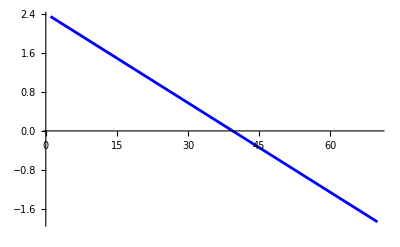

```mathematica
Plot[Log[-Log[yg[x,fa,fc,fy0]/fc]],{x,1,70}, PlotStyle->{Blue,Thickness->0.005}]
```

## Kvadratno odstupanje

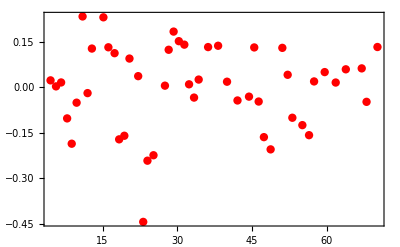

```mathematica
my=lyg[tt,gfa,gfc,gfy0];
residual=my-lny;
tmp={tt,residual};
res=Transpose[tmp];
ListPlot[res,Frame->True,PlotStyle->{PointSize[0.015],RGBColor[1,0,0]}]
```

```mathematica
(residual.residual)/Length[residual]
```

0.0198408

## Podaci i von Bertalanffyjev model

```mathematica
DSolve[{y'[x]==a y[x] ^(2/3)(1- (y[x]/C)^(1/3)),y[0]==y0},y[x],x]
```

```mathematica
DSolve[{y'[x]==a y[x] ^(2/3)-b y[x],y[0]==y0},y[x],x]
```

```mathematica
DSolve[{z'[x]==a/3 -b/3 z[x],z[0]==z0},z[x],x]
```

{{z[x]→(ⅇ^(-(b x)/3) (-a+a ⅇ^((b x)/3)+b z0))/b}}

```mathematica
yb[x_,a_,c_,z0_]:= c(1-z0 Exp[-a x/(3 c^(1/3))])^3
```

```mathematica
lyb[x_,a_,c_,z0_]:= Log[c(1-z0 Exp[-a x/(3 c^(1/3))])^3]
```

```mathematica
yb[x_,a_,c_,z0_]:= (c(1-z0 Exp[-a x/(3 c)]))^3
```

```mathematica
lyb[x_,a_,c_,z0_]:= 3 Log[c(1-z0 Exp[-a x/(3 c)])]
```

```mathematica
par1=FindFit[data,{yb[x,a,c,z0],{a>0,z0>0,c>0}},{{a,1},{c,24},{z0,0.1}},x,MaxIterations->5000]
```

{a→0.0965442,c→25.5105,z0→0.96843}

```mathematica
par1=FindFit[data,{yb[x,a,c,z0],{a>0,c>0,z0>0}},{{a,2},{c,2},{z0,0.1}},x,MaxIterations->3000]
```

FindFit::eit: The algorithm does not converge to the tolerance of 4.80622×10^-6 in 3000 iterations. The best estimated solution, with feasibility residual, KKT residual, or complementary residual of {0.000010122945905494034`, 0.006213448365937626`, 7.491994893878196`*^-6}, is returned.

{a→0.385707,c→3.03033,z0→1.64672}

```mathematica
par1=FindFit[data,{yb[x,a,c,z0],{a>0,c>0,z0>0}},{{a,10},{c,1},{z0,0.01}},x,MaxIterations->2000]
```

{a→0.385694,c→3.03037,z0→1.64665}

```mathematica
par1a=FindFit[lndata,{lyb[x,a,c,z0],{a>0,c>0,z0>0,yb[4,a,c,z0]>0}},{{a,0.23239},{c,48.4661},{z0,0.01}},x,MaxIterations->15000]
```

FindFit::eit: The algorithm does not converge to the tolerance of 4.80622×10^-6 in 15000 iterations. The best estimated solution, with feasibility residual, KKT residual, or complementary residual of {0.0002738076260011667`, 14.062296618014258`, 0.00010873777160735818`}, is returned.

{a→0.140258,c→7.95269,z0→0.996912}

```mathematica
par1a=FindFit[lndata,{lyb[x,a,c,z0],{a>0,c>0,z0>0,yb[4,a,c,z0]>0}},{{a,0.14025755733450568},{c,7.952694315062227},{z0,0.9969121567895964}},x,MaxIterations->15000]
```

FindFit::eit: The algorithm does not converge to the tolerance of 4.80622×10^-6 in 15000 iterations. The best estimated solution, with feasibility residual, KKT residual, or complementary residual of {9.01426118470795`*^-11, 0.00010036081880387699`, 5.826446629261854`*^-12}, is returned.

{a→0.155367,c→38.3923,z0→1.00376}

```mathematica
par=FindFit[lndata,{lyb[x,a,c,z0],{a>0,c>0,z0>0,yb[4,a,c,z0]>0}},{{a,0.15536683126629539},{c,38.39228545433871},{z0,1.0037616861981937}},x,MaxIterations->15000]
```

FindFit::eit: The algorithm does not converge to the tolerance of 4.80622×10^-6 in 15000 iterations. The best estimated solution, with feasibility residual, KKT residual, or complementary residual of {0.05975247049947897`, 0.457647946906443`, 0.01585908371058561`}, is returned.

{a→0.155367,c→38.3923,z0→1.00376}

```mathematica
par1=FindFit[lndata,{lyb[x,a,c,z0],{a>0,c>0,z0>0,yb[4.2,a,c,z0]>0}},{{a,0.23239},{c,48.4661},{z0,0.01}},x,MaxIterations->5000]
```

FindFit::eit: The algorithm does not converge to the tolerance of 4.80622×10^-6 in 5000 iterations. The best estimated solution, with feasibility residual, KKT residual, or complementary residual of {0.027024403121102034`, 16.9786540323543`, 0.008412650660478664`}, is returned.

{a→0.00288387,c→6.73375,z0→0.743451}

```mathematica
par1=FindFit[lndata,{lyb[x,a,c,z0],{a>0,c>0,z0>0,yb[4.2,a,c,z0]>0}},{{a,0.15536683126629539},{c,38.39228545433871},{z0,1.0037616861981937}},x,MaxIterations->5000]
```

FindFit::eit: The algorithm does not converge to the tolerance of 4.80622×10^-6 in 5000 iterations. The best estimated solution, with feasibility residual, KKT residual, or complementary residual of {0.05446715898212877`, 0.47647108302938956`, 0.014293545774260681`}, is returned.

{a→0.155367,c→38.3923,z0→1.00376}

```mathematica
par1=FindFit[lndata,{lyb[x,a,c,z0],{a>0,c>0,c<50,z0<1}},{{a,0.385},{c,27.8},{z0,0.64}},x,MaxIterations->3000]
```

{a→0.131722,c→50.,z0→1.}

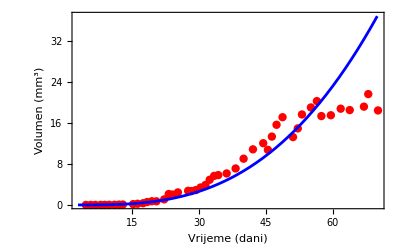

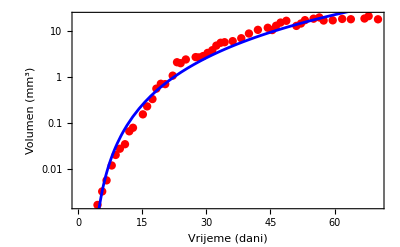

```mathematica
{fa,fc,fz0}={a,c,z0}/. par;c1=Plot[yb[x,fa,fc,fz0],{x,0,70}, PlotRange->{0,25000},PlotStyle->{Blue,Thickness->0.005}];
lc1=LogPlot[yb[x,fa,fc,fz0],{x,0,70}, PlotRange->{0,25000},PlotStyle->{Blue,Thickness->0.005}];
Show[pod,c1]
Show[lpod,lc1]
```

## Kvadratno odstupanje

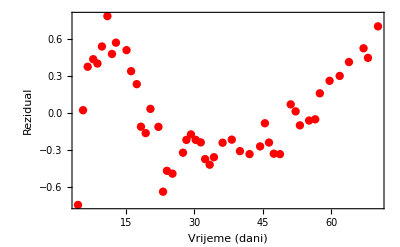

```mathematica
my=lyb[tt,fa,fc,fz0];
residual=my-lny;
tmp={tt,residual};
res=Transpose[tmp];
ListPlot[res,Frame->True,FrameLabel->{"Vrijeme (dani)","Rezidual"},RotateLabel->True,PlotStyle->{PointSize[0.015],RGBColor[1,0,0]}]
```

```mathematica
(residual.residual)/Length[residual]
```

0.136447

## JEDNOSTAVNI MODEL RASTA TUMORA

```mathematica
d=0.7;
c1=ParametricPlot[{Sin[x],Cos[x]},{x,0,2 Pi},Axes->False];
c2=ParametricPlot[{d Sin[x],d Cos[x]},{x,0,2 Pi},Axes->False];
Show[c1,c2]
```